# Investigating the capture cases for b=0.4

## Orbital parameters, equations of motion, and others

Our initial conditions consists of the vertical line in cylindrical coordinates (R,z) = (3,z). Note that in the absence of the magnetic field, R=3 (and z=0) refer to the innermost stable circular orbit of the Schwarzschild black hole (in the units used in the paper). We choose l to correspond to a circular orbit located at ρ=3. This restricts the value of l to be

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
```

The equations of motion are

```mathematica
ddrho[b_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[b]b-1)/(2 ρ[σ]^2)+(l[b]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[b_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[b]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b^2 Sin[θ[σ]]Cos[θ[σ]]
```

Since we have two 2nd order differential equations, we need to have four initial conditions in total, (ρ[0],ρ'[0],θ[0],θ'[0]), subject to the energy constraint given in the paper. We choose our initial conditions in cylindrical coordinates to be the line (R,z) = (3,z) and with initial shooting angle ϕ_sh ∈ [0,2π]. We make functions that take as input z and ϕ_sh and outputs the corresponding initial conditions (ρ[0],ρ'[0],θ[0],θ'[0]) in spherical coordinates.

```mathematica
getInitConditions[b_,en_,z_,ϕsh_]:=Module[{ρ0,θ0,Ueff,dρ0,dθ0,result},
ρ0=√(9+z^2);
θ0=ArcTan[z,3];
Ueff=(1-1/ρ0)(1+((l[b]-b (ρ0 Sin[θ0])^2)^2)/(ρ0 Sin[θ0])^2);
dρ0=(√((en^2-Ueff)/(Cos[θ0-ϕsh]^2+ρ0(ρ0-1)Sin[θ0-ϕsh]^2)))Cos[θ0-ϕsh];
dθ0=-(√((en^2-Ueff)/(Cos[θ0-ϕsh]^2+ρ0(ρ0-1)Sin[θ0-ϕsh]^2)))Sin[θ0-ϕsh];
result={ρ0,dρ0,θ0,dθ0}
];
```

Note that if we choose the the energy to be such that en^2>U_crit then the way we choose initial conditions always yields us energetically allowed initial conditions.

## Basin Calculation Preliminaries

We have the following tests: (z > 1000) → 1, (z < -1000) → 2, (ρ ≤ 1) → 3 and (σ >MaximumT) → 4

```mathematica
Attractors = {WhenEvent[ρ[σ]Cos[θ[σ]]>1000,Throw[1]],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,Throw[2]],WhenEvent[ρ[σ]≤ 1,Throw[3]],WhenEvent[σ>MaximumT,Throw[4]]};
```

Next, we make a function that takes initial conditions (z, ϕsh) and outputs its final state according to the scheme above:

```mathematica
CheckAttractor[b_,en_,z_,ϕsh_]:=Module[{initConditions},
initConditions=getInitConditions[b,en,z,ϕsh];
Catch[
NDSolve[{ddθ[b],ddrho[b],ρ[0]==initConditions⟦1⟧,ρ'[0]==initConditions⟦2⟧,θ[0]==initConditions⟦3⟧,θ'[0]==initConditions⟦4⟧}~Join~Attractors,{ρ,θ},{σ,0,MaximumT+1}];
]
];
```

We assign the corresponding colors

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0]}

In the calculations that proceed, this varies between 0 and 1, and gives a general feel how near completion the current task is.

Finally we set the maximum integration time, the number of pixels and the basin region. We always check in the region z ∈ [-5,5] and ϕsh ∈ [0,2π].

```mathematica
MaximumT = 10^6;pixels=500;Regionz=Subdivide[5,-5,pixels];Regionϕsh=Subdivide[-π,π,pixels];
```

## Positive l: ε=1.2

If you calculate ε_cap=√U_cap in this case, it turns out to be ε_cap=1.30528>1.2 (see Energetic calculations.nb), hence it should be impossible to have capture cases.

```mathematica
$IsPositive=True;ε=1.2;
```

```mathematica
b=0.4;
```

```mathematica
CheckAttractor[b,ε,Regionz⟦42⟧,Regionϕsh⟦8⟧]
```

3

The above should be impossible. Let us investigate by looking at the energy of this trajectory.

```mathematica
initConditions1=getInitConditions[b,ε,Regionz⟦42⟧,Regionϕsh⟦8⟧]
```

{(17 √229)/50,-0.271805,ArcTan[150/209],0.160919}

```mathematica
stopConditions={WhenEvent[ρ[σ]≤1,endt=σ;"StopIntegration"],WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,endt=σ;"StopIntegration"],WhenEvent[σ>MaximumT,endt=σ;"StopIntegration"]};
```

```mathematica
sol=NDSolve[{ddθ[b],ddrho[b],ρ[0]==initConditions1⟦1⟧,ρ'[0]==initConditions1⟦2⟧,θ[0]==initConditions1⟦3⟧,θ'[0]==initConditions1⟦4⟧}~Join~stopConditions,{ρ,θ},{σ,0,MaximumT+1}];
```

```mathematica
en[b_]:=√(ρ'[σ]^2+ρ[σ](ρ[σ]-1)θ'[σ]^2+(1-1/ρ[σ])(1+((l[b]-b ρ[σ]^2 Sin[θ[σ]]^2)^2)/(ρ[σ]^2 Sin[θ[σ]]^2)));
```

```mathematica
enFun=en[0.4]/.First@sol;
```

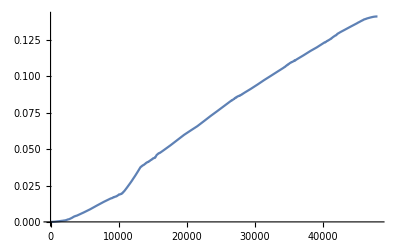

```mathematica
Plot[Abs[enFun-1.2],{σ,0,endt}]
```

The errors grow very large in this case. We try to include MaxSteps →Infinity option

```mathematica
sol2=NDSolve[{ddθ[b],ddrho[b],ρ[0]==initConditions1⟦1⟧,ρ'[0]==initConditions1⟦2⟧,θ[0]==initConditions1⟦3⟧,θ'[0]==initConditions1⟦4⟧}~Join~stopConditions,{ρ,θ},{σ,0,MaximumT+1},MaxSteps->Infinity];
```

```mathematica
enFun2=en[0.4]/.First@sol2;
```

```mathematica
Plot[Abs[enFun-1.2],{σ,0,endt}]
```

-Graphics-

No change. We try to increase WorkingPrecision

```mathematica
sol3=NDSolve[{ddθ[b],ddrho[b],ρ[0]==initConditions1⟦1⟧,ρ'[0]==initConditions1⟦2⟧,θ[0]==initConditions1⟦3⟧,θ'[0]==initConditions1⟦4⟧}~Join~stopConditions,{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25,MaxSteps->Infinity];
```

NDSolve::precw: The precision of the differential equation ({{θ''[σ]==-0.16 Cos[θ[σ]] Sin[θ[σ]]+(15.2329 Cot[θ[σ]] Csc[θ[«1»]]^2)/ρ[σ]^4-(2 θ'[σ] ρ'[σ])/ρ[σ],ρ''[σ]==1.06118/ρ[σ]^2+(7.61647 Csc[θ[«1»]]^2 (-3+2 ρ[«1»]))/ρ[σ]^4-0.08 Sin[θ[«1»]]^2 (-1+2 ρ[«1»])+1/2 (-3+2 ρ[«1»]) θ'[σ]^2,ρ[0]==(17 √229)/50,ρ'[0]==-0.271805,θ[0]==ArcTan[150/209],θ'[0]==0.160919},{},{},{},{WhenEvent[ρ[σ]≤1,endt=σ;StopIntegration],WhenEvent[Abs[ρ[σ] Cos[θ[«1»]]]>1000,endt=σ;StopIntegration],WhenEvent[σ>MaximumT,endt=σ;StopIntegration]}}) is less than WorkingPrecision (25.).

```mathematica
enFun3=en[0.4]/.First@sol3;
```

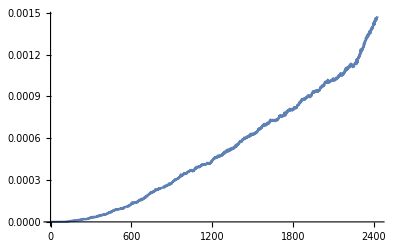

```mathematica
Plot[Abs[enFun-1.2],{σ,0,endt}]
```

The error is better. We look at its final case

```mathematica
ρ[endt]Cos[θ[endt]]/.sol3
```

{1000.}

This means that the trajectory is correctly considered to escape to z→ +∞. We also check the apparent bounded cases

```mathematica
CheckAttractor[b,ε,Regionz⟦378⟧,Regionϕsh⟦79⟧]
```

2

```mathematica
CheckAttractor[b,ε,Regionz⟦394⟧,Regionϕsh⟦334⟧]
```

2

Weird. According to the saved data (see BasinEntropyExample.nb), these correspond to black pixels.

Since the data is being weird, our solution will be to separately calculate the weird pixels in a separate notebook, then alter the matrices in the final basin plots.